#### Kamen setup

```mathematica
kamen[x_]:=0.96-0.25(x-0.5)^2
FindRoot[kamen[x],{x,-2}]
```

{x→-1.45959}

```mathematica
{x->-1.4595917942265424}
```

```mathematica
{x->2.4595917942265424}
```

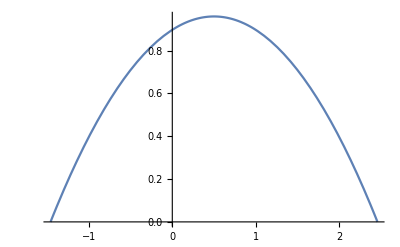

```mathematica
kamenPlot=Plot[kamen[x],{x,-1.4595917942265424,2.4595917942265424}]
```

#### String setup

```mathematica
k=1;
g=-1;
boundaryHeightLeft=11;
boudaryHeightRight=1;
boundaryLeft =-1;
boundaryRight=2;
nXPoints=30;(* Tu klameme, nepocitame totiz bod v "boudaryLeft". Takze oficialne este je o jeden bod naviac. *)

(* Finite difference method - rozdelime x-ovu os na bodiky, v tychto bodoch pocitame "y" *)
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```

Toto navadza na sustavu rovnic -> matica*y=hodnoty, kde pozname maticu a hodnoty: (vid text)

```mathematica
(* Opisanie matice a vektora podla textu *)
matica = 1/dx^2* Table[If[i==j,2, If[Abs[i-j]==1,-1,0]],{i,0,nXPoints},{j,0,nXPoints}];
hodnoty = Table[-1+If[i==0 || i==nXPoints,1/dx^2,0],{i,0,nXPoints}];

(* Sustavu treba vyriesit. Kedze je to ilustracne, tak pouzivam LinearSolve, ale inak by sme to mali robit prave asi tym Newtonom, alebo ako. *)
ypsilony = LinearSolve[matica,hodnoty];
```

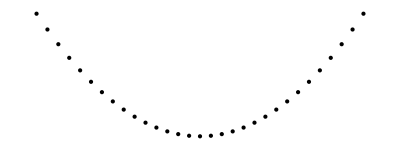

```mathematica
(* Transpose[{xPoints,ypsilony}]; *)
(* Previsnute body bez väzieb. *)
body = Graphics[Point[Transpose[{xPoints,ypsilony}]]]
```

#### Praca s kamenom a String-om - funguje tu zatial iba ten PLOT, kam by sme mohli hodit vsetky veci dokopy.

```mathematica
psi[y_]:=1/2*k*(D[y,x])^2-g*y;
potential[y_]:=Integrate[psi[y],{x,0,1}];
psi[y[x]];
potential[y[x]];
```

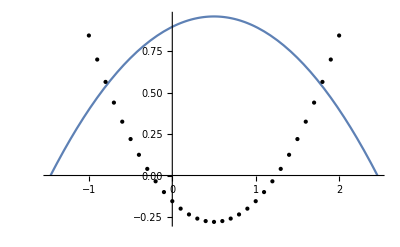

```mathematica
Show[kamenPlot, body, PlotRange->All]
```

```mathematica
ycords=Table[Subscript[y,i],{i,1,nXPoints-1}];
lambdas = Table[Subscript[λ,i],{i,1,nXPoints-1}];
ρ=10;
```

```mathematica
functions2[list_]:=Table[(-list[[i-1]]+2*list[[i]]-list[[i+1]])/dx^2+ 1+Piecewise[{{list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{0,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,2,nXPoints-2}];
functions4[list_]:=Table[Piecewise[{{(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{-list[[nXPoints-1+i]]/ρ,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,1,nXPoints-1}];
functions1[list_]:={(-1+2*list[[1]]-list[[2]])/dx^2+ 1+Piecewise[{{list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]]),list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])<=0},{0,list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])>0}}]}
functions3[list_]:={(-list[[nXPoints-2]]+2*list[[nXPoints-1]]-1)/dx^2+ 1+Piecewise[{{list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]]),list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])<=0},{0,list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])>0}}]}
```

```mathematica
J[x_]:=D[Join[functions1[Join[ycords, lambdas]],functions2[Join[ycords, lambdas]],functions3[Join[ycords, lambdas]],functions4[Join[ycords, lambdas]]],{Join[ycords, lambdas]}]/.Table[Rule[Join[ycords, lambdas][[i]],x[[i]]],{i,1,2*nXPoints-2}]
Newton[x0_]:=NestWhile[LinearSolve[J[#],-Join[functions1[#],functions2[#],functions3[#],functions4[#]]]+#&,x0,Norm[#]>0.000001&,1,10]
```

```mathematica
sol=Newton[Table[0.5,{i,1,2*nXPoints-2}]]
```

{0.945556,0.901111,0.866667,0.842222,0.827778,0.823333,0.828889,0.844444,0.87,0.8975,0.92,0.9375,0.95,0.9575,0.96,0.9575,0.95,0.9375,0.92,0.8975,0.87,0.844444,0.828889,0.823333,0.827778,0.842222,0.866667,0.901111,0.945556,0.,0.,0.,0.,0.,0.,0.,0.,-0.805556,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-0.805556,0.,0.,0.,0.,0.,0.,0.,0.}

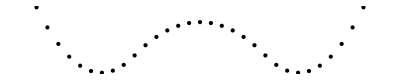

```mathematica
body2 = Graphics[Point[Transpose[{xPoints,Join[{1},sol[[;;nXPoints-1]],{1}]}]]]
```

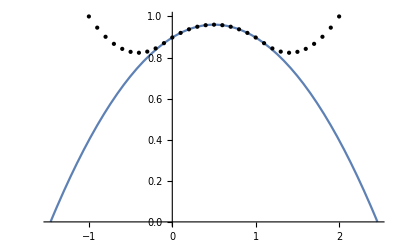

```mathematica
Show[kamenPlot, body2, PlotRange->All]
```

```mathematica
(*Jej supr, vypadá to, že jen nekopíruje tu parabolu, takže to asi něco počítá :D*)
```